## Build Covariance Matrix

```mathematica
M = {{-(2*κ+k)/γ,0},{δ*κ/γ,-k/γ}};
```

```mathematica
MatrixForm[M]
```

((-k-2 κ)/γ | 0
(δ κ)/γ | -k/γ)

```mathematica
expM = MatrixExp[M*(t-tp)];
```

```mathematica
cov = Integrate[expM.{{4*T/γ,0},{0,T/(γ)*(1-δ^2)}}.Transpose[expM],{tp,-∞,t},Assumptions->{γ>0,k>0,κ>0}];
```

{{(2 T)/(k+2 κ),(T δ κ)/((k+κ) (k+2 κ))},{(T δ κ)/((k+κ) (k+2 κ)),1/2 T (1/k+δ^2 (-2/(k+κ)+1/(k+2 κ)))}}

```mathematica
cov = Simplify[cov]
```

{{(2 T)/(k+2 κ),(T δ κ)/((k+κ) (k+2 κ))},{(T δ κ)/((k+κ) (k+2 κ)),1/2 T (1/k+δ^2 (-2/(k+κ)+1/(k+2 κ)))}}

```mathematica
P[R_,r_,kk_] := Simplify[Exp[-1/2*{r,R}.Inverse[cov].{r,R}]]/.{k-> kk};
```

```mathematica
P[1,1,1]
```

ⅇ^(-((1+κ) (-5+δ^2+(-7+4 δ+3 δ^2) κ-2 κ^2))/(4 T (-1+δ^2+2 (-1+δ^2) κ-κ^2)))

## Patching and Normalisation

```mathematica
SubMinus[k]=2*Subscript[u, 0]/(L^2);
```

(2 u_0)/L^2

```mathematica
SubPlus[k]= 2*Subscript[u, 0]/(l^2);
```

(2 u_0)/l^2

```mathematica
SubMinus[f]= Simplify[Integrate[P[R,r,SubMinus[k]],{r,-∞,∞},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}];
```

-(ⅇ^(-(2 R^2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(L^2 T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √(2 π) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)

```mathematica
SubPlus[f]= Simplify[Integrate[P[R,r,SubPlus[k]],{r,-∞,∞},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}];
```

-(ⅇ^(-(2 R^2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(l^2 T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √(2 π) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)

```mathematica
SubMinus[int] = Simplify[Integrate[SubMinus[f],{R,-L,0},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0}]];
```

(L^2 π T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))])/(2 (L^2 κ+2 u_0) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))

```mathematica
SubPlus[int] = Simplify[Integrate[SubPlus[f],{R,0,l},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}]];
```

(l^2 π T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))])/(2 (l^2 κ+2 u_0) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))

```mathematica
{{SubMinus[exprA],SubPlus[exprA]}}=Simplify[Solve[SubMinus[A]*(SubMinus[f]/.{R-> 0})==SubPlus[A]*(SubPlus[f]/.{R-> 0}) && SubMinus[A]*SubMinus[int]+SubPlus[A]*SubPlus[int]==1,{SubMinus[A],SubPlus[A]}],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,0<δ<1,T>0,l>0}];
```

{{A_-→(2 √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(L π T (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/((L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/((l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))),A_+→-((2 u_0 (l^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √((T (l^2 κ+u_0) (L^2 κ+u_0) (L^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))/(l π T (-4 (-1+δ^2) u_0^3 (L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))+l^2 L^2 κ^3 (L^3 Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l^3 Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))-2 (-1+δ^2) κ u_0^2 (L (l^2+3 L^2) Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l (3 l^2+L^2) Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0)))+κ^2 u_0 (L^3 (2 L^2-3 l^2 (-1+δ^2)) Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (l^2 κ+u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(l^2 κ+2 u_0))+l^3 (2 l^2-3 L^2 (-1+δ^2)) Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T u_0 (L^2 κ+u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))/(L^2 κ+2 u_0))))))}}

```mathematica
SubMinus[exprA]=SubMinus[A]->Simplify[(SubPlus[f]/(SubMinus[f]*SubPlus[int]+SubPlus[f]*SubMinus[int]))/.{R->0}];
```

A_-→(l √(2 π) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/((-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))))

```mathematica
SubPlus[exprA]=SubPlus[A]->Simplify[(SubMinus[f]/(SubMinus[f]*SubPlus[int]+SubPlus[f]*SubMinus[int]))/.{R->0}];
```

A_+→(L √(2 π) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/((-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (L^2 κ+u_0))/(-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) √(-(u_0 (l^2 κ+u_0))/(-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2)))))

## Current

```mathematica
Subscript[J, R]= Simplify[-k*R/γ*P[R,r,k]+δ*κ*r/γ*P[R,r,k]-T*(1-δ^2)/(2*γ)*D[P[R,r,k],R]];
```

(ⅇ^(-((k+κ) (k^2 (-4 R^2+r^2 (-1+δ^2))+k (-4 R^2+4 r R δ+3 r^2 (-1+δ^2)) κ-2 r^2 κ^2))/(4 T (k^2 (-1+δ^2)+2 k (-1+δ^2) κ-κ^2))) δ κ (k^2 (r-r δ^2)+k (-2 R δ-3 r (-1+δ^2)) κ+2 r κ^2))/(2 γ (-k^2 (-1+δ^2)-2 k (-1+δ^2) κ+κ^2))

```mathematica
{{SubMinus[exprr]}}= FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R->- L,k-> SubMinus[k]})==0,r],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0}];
```

{{r→-(2 L^3 δ κ u_0)/(L^4 κ^2-(-1+δ^2) u_0 (3 L^2 κ+2 u_0))}}

```mathematica
{{SubPlus[exprr]}}= FullSimplify[Solve[(Subscript[J, R]/P[R,r,k]/.{R-> l,k-> SubPlus[k]})==0,r],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}];
```

{{r→(2 l^3 δ κ u_0)/(l^4 κ^2-(-1+δ^2) u_0 (3 l^2 κ+2 u_0))}}

```mathematica
Subscript[J, left]=Integrate[SubMinus[A]*Subscript[J, R]/.{R-> -L,k-> SubMinus[k],SubMinus[exprA]},{r,-∞,r/. SubMinus[exprr]},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubMinus[k]>0,T>0}];
```

-((ⅇ^(-(2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √(2 π) T δ κ (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/(L^2 γ (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) (κ^2-(4 (-1+δ^2) κ u_0)/L^2-(4 (-1+δ^2) u_0^2)/L^4) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))))

```mathematica
Subscript[J, right]=Integrate[SubPlus[A]*Subscript[J, R]/.{R-> l,k-> SubPlus[k],SubPlus[exprA]},{r,r/.{SubPlus[exprr]},Infinity},Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,l>0,δ<1,δ>0,SubPlus[k]>0,T>0}];
```

(ⅇ^(-(2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √(2 π) T δ κ (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/(l^2 γ (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2) (κ^2-(4 (-1+δ^2) κ u_0)/l^2-(4 (-1+δ^2) u_0^2)/l^4) ((l L^2 π^(3/2) T Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-L^4 κ^2+4 L^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/(√2 (L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))+(l^2 L π^(3/2) T Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √(-(T (-l^4 κ^2+4 l^2 (-1+δ^2) κ u_0+4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/(√2 (l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))))

```mathematica
Subscript[J, total]= Simplify[Subscript[J, left]+ Subscript[J, right],Assumptions->{Subscript[u, 0]>0,κ>0,γ>0,L>0,δ<1,δ>0,SubMinus[k]>0,T>0,l>0,SubPlus[k]>0}];
```

-((2 δ κ (-((ⅇ^(-(2 u_0 (L^2 κ+u_0) (L^2 κ+2 u_0))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) L √((T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(l^2 κ+2 u_0)))/((L^2 κ+2 u_0) (-l^4 κ^2+3 l^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2)))+(ⅇ^(-(2 u_0 (l^2 κ+u_0) (l^2 κ+2 u_0))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))) l √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(L^2 κ+2 u_0)))/((l^2 κ+2 u_0) (-L^4 κ^2+3 L^2 (-1+δ^2) κ u_0+2 (-1+δ^2) u_0^2))))/(π γ ((L Erf[√2 √((u_0 (L^4 κ^2+3 L^2 κ u_0+2 u_0^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 u_0+6 l^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 l^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (L^2 κ+u_0) (l^2 κ+2 u_0))))/((L^2 κ+2 u_0) (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2))+(l Erf[√2 √((u_0 (l^4 κ^2+3 l^2 κ u_0+2 u_0^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ u_0-4 (-1+δ^2) u_0^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 u_0+6 L^4 (3-5 δ^2+2 δ^4) κ^2 u_0^2+20 L^2 (-1+δ^2)^2 κ u_0^3+8 (-1+δ^2)^2 u_0^4))/(u_0 (l^2 κ+u_0) (L^2 κ+2 u_0))))/((l^2 κ+2 u_0) (L^4 κ^2-3 L^2 (-1+δ^2) κ u_0-2 (-1+δ^2) u_0^2)))))

```mathematica
Subscript[J, total]=-((2 δ κ (-((ⅇ^(-(2 Subscript[u, 0] (L^2 κ+Subscript[u, 0]) (L^2 κ+2 Subscript[u, 0]))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))) L √(1/(l^2 κ+2 Subscript[u, 0])T (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 l^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 l^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4)))/((L^2 κ+2 Subscript[u, 0]) (-l^4 κ^2+3 l^2 (-1+δ^2) κ Subscript[u, 0]+2 (-1+δ^2) Subscript[u, 0]^2)))+(ⅇ^(-(2 Subscript[u, 0] (l^2 κ+Subscript[u, 0]) (l^2 κ+2 Subscript[u, 0]))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))) l √((T (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 L^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 L^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(L^2 κ+2 Subscript[u, 0])))/((l^2 κ+2 Subscript[u, 0]) (-L^4 κ^2+3 L^2 (-1+δ^2) κ Subscript[u, 0]+2 (-1+δ^2) Subscript[u, 0]^2))))/(π γ ((L Erf[√2 √((Subscript[u, 0] (L^4 κ^2+3 L^2 κ Subscript[u, 0]+2 Subscript[u, 0]^2))/(T (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))] √((T (L^4 κ^2-4 L^2 (-1+δ^2) κ Subscript[u, 0]-4 (-1+δ^2) Subscript[u, 0]^2) (l^8 κ^4-7 l^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 l^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 l^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(Subscript[u, 0] (L^2 κ+Subscript[u, 0]) (l^2 κ+2 Subscript[u, 0]))))/((L^2 κ+2 Subscript[u, 0]) (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2))+(l Erf[√2 √((Subscript[u, 0] (l^4 κ^2+3 l^2 κ Subscript[u, 0]+2 Subscript[u, 0]^2))/(T (l^4 κ^2-3 l^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))] √((T (l^4 κ^2-4 l^2 (-1+δ^2) κ Subscript[u, 0]-4 (-1+δ^2) Subscript[u, 0]^2) (L^8 κ^4-7 L^6 (-1+δ^2) κ^3 Subscript[u, 0]+6 L^4 (3-5 δ^2+2 δ^4) κ^2 Subscript[u, 0]^2+20 L^2 (-1+δ^2)^2 κ Subscript[u, 0]^3+8 (-1+δ^2)^2 Subscript[u, 0]^4))/(Subscript[u, 0] (l^2 κ+Subscript[u, 0]) (L^2 κ+2 Subscript[u, 0]))))/((l^2 κ+2 Subscript[u, 0]) (L^4 κ^2-3 L^2 (-1+δ^2) κ Subscript[u, 0]-2 (-1+δ^2) Subscript[u, 0]^2)))));
```

## Simplifying Notation

```mathematica
Subscript[J, total]= Subscript[J, total]/.{κ->κ*2*T/(l+L)^2};
```

```mathematica
Subscript[J, total]= Subscript[J, total]/.{T->Subscript[u, 0]*T};
```

```mathematica
Subscript[J, total]= Simplify[Subscript[J, total],{γ>0,l>0,L>0,δ>0,T>0,Subscript[u, 0]>0,κ>0}];
```

```mathematica
Subscript[J, simp]= Subscript[J, total]/.{δ->(-Subscript[T, 1]+Subscript[T, 2])/(Subscript[T, 1]+Subscript[T, 2]),T->(Subscript[T, 1]+Subscript[T, 2])/2};
```

```mathematica
Subscript[J, pot]=FullSimplify[Subscript[J, simp]/.{γ->0.01,l->9.0,L->1.0,Subscript[T, 1]->0.1,Subscript[T, 2]->1,Subscript[u, 0]->u}];
```

```mathematica
Subscript[J, sub] = Simplify[Subscript[J, simp]/.{γ->0.01,l->9.0,L->1.0,Subscript[T, 1]->0.1,Subscript[T, 2]->T,Subscript[u, 0]->1},{T>0}];
```

## Importing Data

```mathematica
dt1 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt1","List"];
```

```mathematica
dt5 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt5","List"];
```

```mathematica
dt10 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt10","List"];
```

```mathematica
dt15 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt15","List"];
```

```mathematica
dt20 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_dt20","List"];
```

```mathematica
tvals = Array[#&,100,{0.1,1.1}];
```

```mathematica
pl1 = ListPlot[{Transpose@{tvals,dt15},Transpose@{tvals,dt20}}];
```

```mathematica
th1 = Plot[{Subscript[J, sub]/.{κ->15},Subscript[J, sub]/.{κ->20}},{T,0.1,1.1}];
```

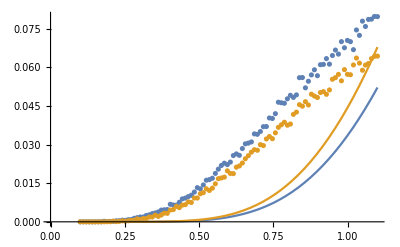

```mathematica
Show[pl1,th1]
```

```mathematica
u1 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u1","List"];
```

```mathematica
u5 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u5","List"];
```

```mathematica
u10 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u10","List"];
```

```mathematica
u15 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u15","List"];
```

```mathematica
u20 = Import["/home/ieshghi/Documents/code/dumbbell/data/parab_strongk/sl_u20","List"];
```

```mathematica
uvals = Array[#&,100,{0,5}];
```

```mathematica
pl2 = ListPlot[{Transpose@{uvals,u5},Transpose@{uvals,u10}}];
```

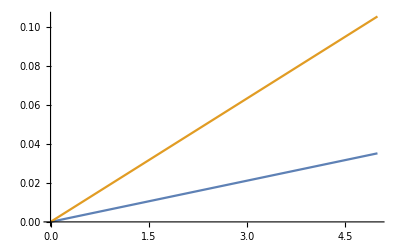

```mathematica
th2 = Plot[{Subscript[J, pot]/.{κ->5},Subscript[J, pot]/.{κ->10}},{u,0,5}]
```

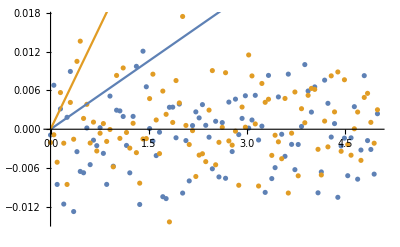

```mathematica
Show[pl2,th2]
```